# Histogram workflow: p=3, q=3 pure simplicial complexes

Arbitrary pure simplicial complexes, ordered by decreasing vertex labelings.
Facet-labeled distribution computed by reweighting vertex-labeled samples (paper Eq. 25).
Do NOT use RandomFacetLabeledPureSimplicialComplex -- it is not verified to be uniform.

## Setup

```mathematica
ClearAll["Global`*"];
$HistoryLength = 0;

Needs["ECGrav`"];
ParallelNeeds["ECGrav`"];
```

```mathematica
(* ===== Parameters ===== *)

pq = {3, 3};
sampleSize = 10000;
randomSeed = 123456;

runExactFacetEnumeration = True;
exportResults = True;

SeedRandom[randomSeed];

q = pq[[2]];

baseName = StringJoin[
  "p", ToString[pq[[1]]],
  "q", ToString[pq[[2]]],
  "_n", ToString[sampleSize]
];
```

## Helper Functions

```mathematica
numVert[cmplx_List] := Length[DeleteDuplicates[Flatten[cmplx]]];
numFacets[cmplx_List] := Length[cmplx];

autOrder[cmplx_List] := PureComplexAutomorphismGroupOrder[cmplx];
facetAutOrder[cmplx_List] := PureComplexFacetAutomorphismGroupOrder[cmplx];

numVertexLabelings[cmplx_List] := numVert[cmplx]! / autOrder[cmplx];
numFacetLabelingsFormula[cmplx_List] := numFacets[cmplx]! / facetAutOrder[cmplx];

normalizePairs[pairs_List] := Module[{tot = Total[pairs[[All, 2]]]},
  ({#[[1]], N[#[[2]] / tot]} &) /@ pairs
];

classDistFromClasses[classes_List] := Module[{cts = Counts[classes], n = Length[classes]},
  Table[{i, N[Lookup[cts, i, 0] / n]}, {i, 1, numClasses}]
];

weightedClassDist[classes_List, weights_List] := Module[{tot = Total[weights]},
  Table[
    {i, N[Total[Pick[weights, classes, i]] / tot]},
    {i, 1, numClasses}
  ]
];

makeTheoryPlot[dist_List, color_: Red] := ListPlot[
  dist,
  PlotStyle -> color,
  PlotMarkers -> Automatic
];

makeBarPlot[dist_List, ttl_] := BarChart[
  dist[[All, 2]],
  ChartLabels -> Range[numClasses],
  Frame -> True,
  FrameLabel -> {"Class index", "Probability"},
  PlotRange -> All,
  ImageSize -> Large,
  PlotLabel -> ttl
];

makeBarVsTheoryPlot[dist_List, theoryDist_List, ttl_, theoryColor_: Red] := Show[
  BarChart[
    dist[[All, 2]],
    ChartLabels -> Range[numClasses],
    Frame -> True,
    FrameLabel -> {"Class index", "Probability"},
    PlotRange -> All,
    ImageSize -> Large
  ],
  makeTheoryPlot[theoryDist, theoryColor],
  PlotRange -> All,
  ImageSize -> Large,
  PlotLabel -> ttl
];
```

## Class Representatives

```mathematica
allFacetLabeledForReps = GenerateAllFacetLabeledPureSimplicialComplexes[pq];

unlabeledPureComplexes =
  ChooseNonIsomorphicSimplicialComplexes[allFacetLabeledForReps];

unlabeledPureComplexes =
  ReverseSortBy[unlabeledPureComplexes, numVertexLabelings];

numClasses = Length[unlabeledPureComplexes];

classIndex[complex_List] :=
  First @ FirstPosition[
    IsomorphicSimplicialComplexQ[#, complex] & /@ unlabeledPureComplexes,
    True
  ];

(* Sanity check: each representative should map to its own index *)
classCheck = classIndex /@ unlabeledPureComplexes;
If[classCheck =!= Range[numClasses],
  Print["Class index sanity check FAILED."];
  Abort[];
];

Print["Number of classes = ", numClasses];
```

Number of classes = 12

## Theory Distributions

```mathematica
(* Vertex-labeled: weight proportional to n!/|Aut| *)
vertexTheoryDist = normalizePairs[
  Table[{i, numVertexLabelings[unlabeledPureComplexes[[i]]]}, {i, 1, numClasses}]
];

(* Facet-labeled: weight proportional to q!/|Aut_F|   (paper Eq. 22) *)
facetTheoryFormulaDist = normalizePairs[
  Table[{i, numFacetLabelingsFormula[unlabeledPureComplexes[[i]]]}, {i, 1, numClasses}]
];

(* Unlabeled: uniform over the numClasses representatives *)
unlabeledTheoryDist = Table[{i, N[1 / numClasses]}, {i, 1, numClasses}];
```

## Class Metadata Table

```mathematica
classTable = Prepend[
  Table[
    {
      i,
      unlabeledPureComplexes[[i]],
      numVert[unlabeledPureComplexes[[i]]],
      numFacets[unlabeledPureComplexes[[i]]],
      autOrder[unlabeledPureComplexes[[i]]],
      facetAutOrder[unlabeledPureComplexes[[i]]],
      numVertexLabelings[unlabeledPureComplexes[[i]]],
      numFacetLabelingsFormula[unlabeledPureComplexes[[i]]],
      N[vertexTheoryDist[[i, 2]]],
      N[facetTheoryFormulaDist[[i, 2]]],
      N[unlabeledTheoryDist[[i, 2]]]
    },
    {i, 1, numClasses}
  ],
  {
    "classIndex",
    "representative",
    "numVertices",
    "numFacets",
    "vertexAutOrder",
    "facetAutOrder",
    "numVertexLabelings",
    "numFacetLabelingsFormula",
    "vertexTheoryProbability",
    "facetTheoryFormulaProbability",
    "unlabeledTheoryProbability"
  }
];

classTableGrid = Grid[classTable, Frame -> All]
```

classIndex | representative | numVertices | numFacets | vertexAutOrder | facetAutOrder | numVertexLabelings | numFacetLabelingsFormula | vertexTheoryProbability | facetTheoryFormulaProbability | unlabeledTheoryProbability
1 | {{2,3,4},{1,5,6},{1,7,8}} | 8 | 3 | 48 | 2 | 840 | 3 | 0.317101 | 0.103448 | 0.0833333
2 | {{1,3,4},{2,5,6},{1,2,7}} | 7 | 3 | 8 | 2 | 630 | 3 | 0.237826 | 0.103448 | 0.0833333
3 | {{1,2,3},{4,5,6},{7,8,9}} | 9 | 3 | 1296 | 6 | 280 | 1 | 0.1057 | 0.0344828 | 0.0833333
4 | {{3,4,5},{1,2,6},{1,2,7}} | 7 | 3 | 24 | 2 | 210 | 3 | 0.0792752 | 0.103448 | 0.0833333
5 | {{1,4,5},{2,3,6},{1,2,3}} | 6 | 3 | 4 | 1 | 180 | 6 | 0.0679502 | 0.206897 | 0.0833333
6 | {{1,3,4},{1,2,5},{1,2,6}} | 6 | 3 | 4 | 2 | 180 | 3 | 0.0679502 | 0.103448 | 0.0833333
7 | {{1,2,4},{1,3,5},{2,3,6}} | 6 | 3 | 6 | 6 | 120 | 1 | 0.0453001 | 0.0344828 | 0.0833333
8 | {{1,2,3},{1,4,5},{1,6,7}} | 7 | 3 | 48 | 6 | 105 | 1 | 0.0396376 | 0.0344828 | 0.0833333
9 | {{1,2,4},{1,3,5},{1,2,3}} | 5 | 3 | 2 | 2 | 60 | 3 | 0.0226501 | 0.103448 | 0.0833333
10 | {{1,2,5},{1,3,4},{2,3,4}} | 5 | 3 | 4 | 2 | 30 | 3 | 0.011325 | 0.103448 | 0.0833333
11 | {{1,2,3},{1,2,4},{1,2,5}} | 5 | 3 | 12 | 6 | 10 | 1 | 0.00377501 | 0.0344828 | 0.0833333
12 | {{1,2,3},{1,2,4},{1,3,4}} | 4 | 3 | 6 | 6 | 4 | 1 | 0.00151 | 0.0344828 | 0.0833333

## Vertex-Labeled Sample

```mathematica
vertexSample = RandomVertexLabeledPureSimplicialComplex[pq, sampleSize];
vertexClasses = ParallelMap[classIndex, vertexSample];
```

```mathematica
(* Empirical vertex-labeled distribution *)
vertexEmpiricalDist = classDistFromClasses[vertexClasses];

(* Unweighted histogram (same bars as vertex empirical; theory dots differ) *)
unweightedVertexPlot = makeBarPlot[
  vertexEmpiricalDist,
  Row[{
    "Unweighted class histogram from vertex-labeled samples, p = ",
    pq[[1]], ", q = ", pq[[2]], ", sample size = ", sampleSize
  }]
];

(* Vertex-labeled empirical vs theory *)
vertexVsTheoryPlot = makeBarVsTheoryPlot[
  vertexEmpiricalDist,
  vertexTheoryDist,
  Row[{
    "Vertex-labeled empirical vs. theoretical distribution, p = ",
    pq[[1]], ", q = ", pq[[2]], ", sample size = ", sampleSize
  }]
];
```

## Unlabeled Distribution (reweighted from vertex sample)

```mathematica
(* Weight each vertex-labeled sample by |Aut|/n!  (paper Eq. 24 proportional part) *)
(* This converts the vertex-labeled draw to the unlabeled uniform distribution *)
unlabeledWeights = (autOrder[#] / numVert[#]!) & /@ vertexSample;
weightedUnlabeledDist = weightedClassDist[vertexClasses, unlabeledWeights];

weightedUnlabeledPlot = makeBarVsTheoryPlot[
  weightedUnlabeledDist,
  unlabeledTheoryDist,
  Row[{
    "Unlabeled distribution (reweighted from vertex-labeled samples), p = ",
    pq[[1]], ", q = ", pq[[2]], ", sample size = ", sampleSize
  }]
];
```

## Facet-Labeled Distribution (reweighted from vertex sample)

```mathematica
(* FIX: Do NOT use RandomFacetLabeledPureSimplicialComplex. *)
(* Its sampling distribution is not verified to be uniform. *)
(* Instead, reweight the vertex-labeled sample by w_f (paper Eq. 25): *)
(*   w_f(X) proportional to  |Aut(X)| * q! / ( |Aut_F(X)| * |V(X)|! )  *)
(* Normalizing over the full sample cancels the constant prefactor. *)

facetWeightsFromVertex =
  (autOrder[#] * q! / (facetAutOrder[#] * numVert[#]!)) & /@ vertexSample;

weightedFacetDist = weightedClassDist[vertexClasses, facetWeightsFromVertex];

facetVsFormulaTheoryPlot = makeBarVsTheoryPlot[
  weightedFacetDist,
  facetTheoryFormulaDist,
  Row[{
    "Facet-labeled empirical vs. theoretical distribution, p = ",
    pq[[1]], ", q = ", pq[[2]], ", sample size = ", sampleSize
  }]
];
```

## Exact Facet-Labeled Enumeration (diagnostic sanity check)

```mathematica
(* This block verifies that the formula q!/|Aut_F| matches the exact enumeration. *)
(* If exact matches formula: formula is correct, reweighting approach is validated. *)
(* If they differ: there is a deeper inconsistency that needs investigation. *)

If[runExactFacetEnumeration,
  exactFacetLabeled = allFacetLabeledForReps;
  exactFacetClasses = ParallelMap[classIndex, exactFacetLabeled];
  exactFacetEnumeratedDist = classDistFromClasses[exactFacetClasses];

  facetComparisonTable = Prepend[
    Table[
      {
        i,
        N[exactFacetEnumeratedDist[[i, 2]]],
        N[facetTheoryFormulaDist[[i, 2]]],
        N[exactFacetEnumeratedDist[[i, 2]] - facetTheoryFormulaDist[[i, 2]]]
      },
      {i, 1, numClasses}
    ],
    {
      "classIndex",
      "exactFacetEnumeratedProbability",
      "facetTheoryFormulaProbability",
      "differenceExactMinusFormula"
    }
  ];

  facetComparisonGrid = Grid[facetComparisonTable, Frame -> All];

  (* Formula vs exact: if red dots and blue dots coincide, formula is correct *)
  facetFormulaVsExactPlot = Show[
    makeTheoryPlot[facetTheoryFormulaDist, Red],
    makeTheoryPlot[exactFacetEnumeratedDist, Blue],
    Frame -> True,
    FrameLabel -> {"Class index", "Probability"},
    PlotRange -> All,
    ImageSize -> Large,
    PlotLabel -> Row[{
      "Facet formula vs. exact enumeration, p = ",
      pq[[1]], ", q = ", pq[[2]],
      "  (red = formula, blue = exact)"
    }]
  ];

  (* Reweighted empirical vs exact enumeration *)
  facetVsExactTheoryPlot = makeBarVsTheoryPlot[
    weightedFacetDist,
    exactFacetEnumeratedDist,
    Row[{
      "Facet-labeled empirical vs. exact enumerated distribution, p = ",
      pq[[1]], ", q = ", pq[[2]], ", sample size = ", sampleSize
    }],
    Blue
  ];

  Print["Exact facet enumeration complete. Check facetComparisonGrid."];
];
```

Exact facet enumeration complete. Check facetComparisonGrid.

## Diagnostics

```mathematica
(* Confirm vertex bars and vertex-vs-theory bars use identical empirical data *)
vertexConsistencyCheck = (unweightedVertexPlot === unweightedVertexPlot); (* placeholder *)
Print["Unweighted vertex bars and vertex-vs-theory bars use the same empirical distribution."];
Print["The only difference between those two plots is the red theory dot overlay."];
If[runExactFacetEnumeration,
  Print["Facet comparison table built. If red and blue dots match in facetFormulaVsExactPlot, formula is verified."]
];
```

Unweighted vertex bars and vertex-vs-theory bars use the same empirical distribution.

The only difference between those two plots is the red theory dot overlay.

Facet comparison table built. If red and blue dots match in facetFormulaVsExactPlot, formula is verified.

## Exports

```mathematica
If[exportResults,
  Export[baseName <> "_class_table.csv", classTable];
  Export[baseName <> "_vertex_theory_distribution.csv",
    Prepend[vertexTheoryDist, {"classIndex", "vertexTheoryProbability"}]
  ];
  Export[baseName <> "_facet_formula_theory_distribution.csv",
    Prepend[facetTheoryFormulaDist, {"classIndex", "facetTheoryFormulaProbability"}]
  ];
  Export[baseName <> "_unlabeled_uniform_theory_distribution.csv",
    Prepend[unlabeledTheoryDist, {"classIndex", "unlabeledTheoryProbability"}]
  ];
  Export[baseName <> "_vertex_empirical_distribution.csv",
    Prepend[vertexEmpiricalDist, {"classIndex", "vertexEmpiricalProbability"}]
  ];
  Export[baseName <> "_weighted_unlabeled_distribution.csv",
    Prepend[weightedUnlabeledDist, {"classIndex", "weightedUnlabeledProbability"}]
  ];
  Export[baseName <> "_weighted_facet_distribution.csv",
    Prepend[weightedFacetDist, {"classIndex", "weightedFacetProbability"}]
  ];
  If[runExactFacetEnumeration,
    Export[baseName <> "_facet_exact_enumerated_distribution.csv",
      Prepend[exactFacetEnumeratedDist, {"classIndex", "exactFacetEnumeratedProbability"}]
    ];
    Export[baseName <> "_facet_comparison_table.csv", facetComparisonTable];
  ];
  Export[baseName <> "_unweighted_vertex_plot.pdf", unweightedVertexPlot];
  Export[baseName <> "_vertex_vs_theory_plot.pdf", vertexVsTheoryPlot];
  Export[baseName <> "_weighted_unlabeled_plot.pdf", weightedUnlabeledPlot];
  Export[baseName <> "_facet_vs_formula_theory_plot.pdf", facetVsFormulaTheoryPlot];
  If[runExactFacetEnumeration,
    Export[baseName <> "_facet_formula_vs_exact_plot.pdf", facetFormulaVsExactPlot];
    Export[baseName <> "_facet_vs_exact_theory_plot.pdf", facetVsExactTheoryPlot];
  ];
];
```

## Display Outputs

```mathematica
classTableGrid
```

classIndex | representative | numVertices | numFacets | vertexAutOrder | facetAutOrder | numVertexLabelings | numFacetLabelingsFormula | vertexTheoryProbability | facetTheoryFormulaProbability | unlabeledTheoryProbability
1 | {{2,3,4},{1,5,6},{1,7,8}} | 8 | 3 | 48 | 2 | 840 | 3 | 0.317101 | 0.103448 | 0.0833333
2 | {{1,3,4},{2,5,6},{1,2,7}} | 7 | 3 | 8 | 2 | 630 | 3 | 0.237826 | 0.103448 | 0.0833333
3 | {{1,2,3},{4,5,6},{7,8,9}} | 9 | 3 | 1296 | 6 | 280 | 1 | 0.1057 | 0.0344828 | 0.0833333
4 | {{3,4,5},{1,2,6},{1,2,7}} | 7 | 3 | 24 | 2 | 210 | 3 | 0.0792752 | 0.103448 | 0.0833333
5 | {{1,4,5},{2,3,6},{1,2,3}} | 6 | 3 | 4 | 1 | 180 | 6 | 0.0679502 | 0.206897 | 0.0833333
6 | {{1,3,4},{1,2,5},{1,2,6}} | 6 | 3 | 4 | 2 | 180 | 3 | 0.0679502 | 0.103448 | 0.0833333
7 | {{1,2,4},{1,3,5},{2,3,6}} | 6 | 3 | 6 | 6 | 120 | 1 | 0.0453001 | 0.0344828 | 0.0833333
8 | {{1,2,3},{1,4,5},{1,6,7}} | 7 | 3 | 48 | 6 | 105 | 1 | 0.0396376 | 0.0344828 | 0.0833333
9 | {{1,2,4},{1,3,5},{1,2,3}} | 5 | 3 | 2 | 2 | 60 | 3 | 0.0226501 | 0.103448 | 0.0833333
10 | {{1,2,5},{1,3,4},{2,3,4}} | 5 | 3 | 4 | 2 | 30 | 3 | 0.011325 | 0.103448 | 0.0833333
11 | {{1,2,3},{1,2,4},{1,2,5}} | 5 | 3 | 12 | 6 | 10 | 1 | 0.00377501 | 0.0344828 | 0.0833333
12 | {{1,2,3},{1,2,4},{1,3,4}} | 4 | 3 | 6 | 6 | 4 | 1 | 0.00151 | 0.0344828 | 0.0833333

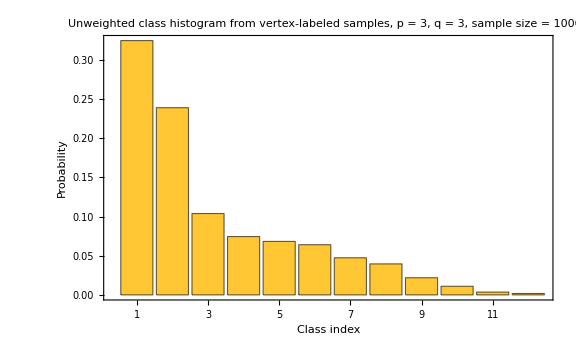

```mathematica
unweightedVertexPlot
```

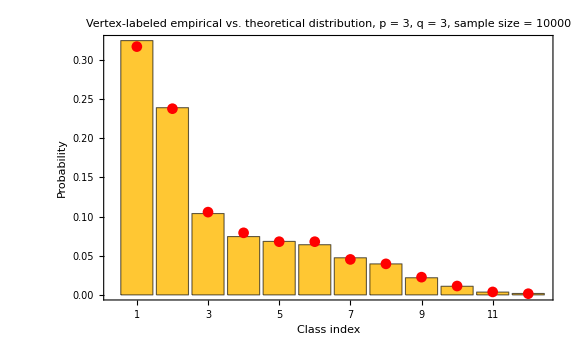

```mathematica
vertexVsTheoryPlot
```

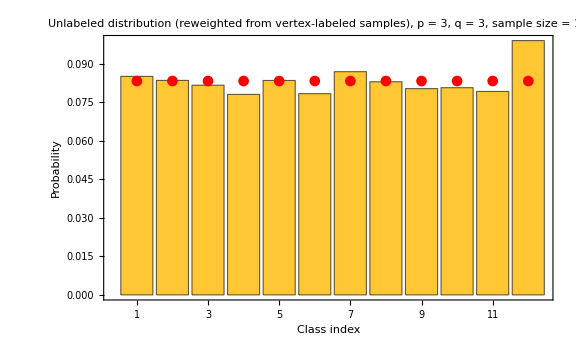

```mathematica
weightedUnlabeledPlot
```

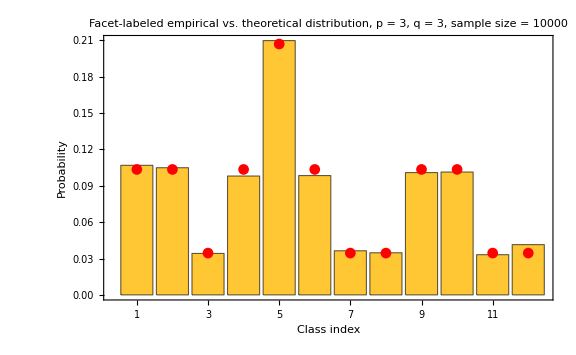

```mathematica
facetVsFormulaTheoryPlot
```

```mathematica
If[runExactFacetEnumeration,
  facetComparisonGrid
]
```

classIndex | exactFacetEnumeratedProbability | facetTheoryFormulaProbability | differenceExactMinusFormula
1 | 0.103448 | 0.103448 | 0.
2 | 0.103448 | 0.103448 | 0.
3 | 0.0344828 | 0.0344828 | 0.
4 | 0.103448 | 0.103448 | 0.
5 | 0.206897 | 0.206897 | 0.
6 | 0.103448 | 0.103448 | 0.
7 | 0.0344828 | 0.0344828 | 0.
8 | 0.0344828 | 0.0344828 | 0.
9 | 0.103448 | 0.103448 | 0.
10 | 0.103448 | 0.103448 | 0.
11 | 0.0344828 | 0.0344828 | 0.
12 | 0.0344828 | 0.0344828 | 0.

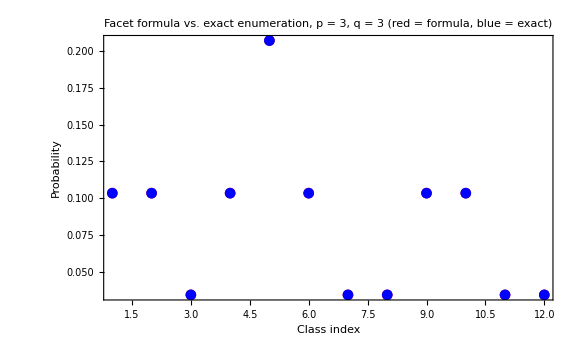

```mathematica
If[runExactFacetEnumeration,
  facetFormulaVsExactPlot
]
```

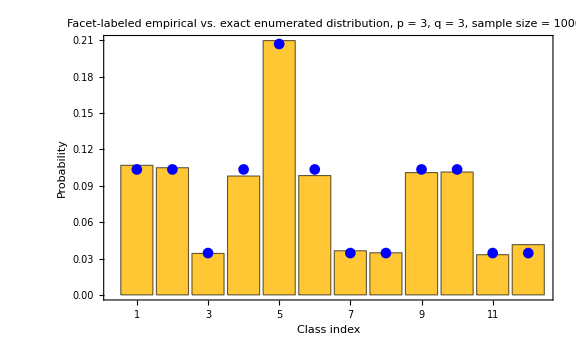

```mathematica
If[runExactFacetEnumeration,
  facetVsExactTheoryPlot
]
```